```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
ViewSurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
plot1=ListPlot3D[data,BoxRatios->Automatic];
plot2=ListPlot[Transpose[Drop[Transpose[data],-1]], PlotRange->{{ 0, 500}, {-500, 500}}];
{plot1,plot2}
]
files= FileNames[];
numbersInString[s_]:=ToExpression@StringCases[s,NumberString]
files = SortBy[files,numbersInString]
allPlots=Table[ViewSurface[file],{file,files}];
(*ListAnimate[allPlots]*)
```

{surface0positive.gpl,surface1positive.gpl,surface2positive.gpl,surface3positive.gpl,surface4positive.gpl,surface5positive.gpl,surface6positive.gpl,surface7positive.gpl,surface8positive.gpl,surface9positive.gpl,surface10positive.gpl,surface11positive.gpl,surface12positive.gpl,surface13positive.gpl,surface14positive.gpl,surface15positive.gpl,surface16positive.gpl,surface17positive.gpl,surface18positive.gpl,surface19positive.gpl,surface20positive.gpl,surface21positive.gpl,surface22positive.gpl,surface23positive.gpl,surface24positive.gpl,surface25positive.gpl,surface26positive.gpl,surface27positive.gpl,surface28positive.gpl,surface29positive.gpl,surface30positive.gpl,surface31positive.gpl,surface32positive.gpl,surface33positive.gpl,surface34positive.gpl,surface35positive.gpl,surface36positive.gpl,surface37positive.gpl,surface38positive.gpl,surface39positive.gpl,surface40positive.gpl,surface41positive.gpl,surface42positive.gpl,surface43positive.gpl,surface44positive.gpl,surface45positive.gpl,surface46positive.gpl,surface47positive.gpl,surface48positive.gpl,surface49positive.gpl,surface50positive.gpl,surface51positive.gpl,surface52positive.gpl,surface53positive.gpl,surface54positive.gpl,surface55positive.gpl,surface56positive.gpl,surface57positive.gpl,surface58positive.gpl,surface59positive.gpl,surface60positive.gpl,surface61positive.gpl,surface62positive.gpl,surface63positive.gpl,surface64positive.gpl,surface65positive.gpl,surface66positive.gpl,surface67positive.gpl,surface68positive.gpl,surface69positive.gpl,surface70positive.gpl,surface71positive.gpl,surface72positive.gpl,surface73positive.gpl,surface74positive.gpl,surface75positive.gpl,surface76positive.gpl,surface77positive.gpl,surface78positive.gpl,surface79positive.gpl,surface80positive.gpl,surface81positive.gpl,surface82positive.gpl,surface83positive.gpl,surface84positive.gpl,surface85positive.gpl,surface86positive.gpl,surface87positive.gpl,surface88positive.gpl,surface89positive.gpl,surface90positive.gpl,surface91positive.gpl,surface92positive.gpl,surface93positive.gpl,surface94positive.gpl,surface95positive.gpl,surface96positive.gpl,surface97positive.gpl,surface98positive.gpl,surface99positive.gpl,surface100positive.gpl,surface101positive.gpl,surface102positive.gpl,surface103positive.gpl,surface104positive.gpl,surface105positive.gpl,surface106positive.gpl,surface107positive.gpl,surface108positive.gpl,surface109positive.gpl,surface110positive.gpl,surface111positive.gpl,surface112positive.gpl,surface113positive.gpl,surface114positive.gpl,surface115positive.gpl,surface116positive.gpl,surface117positive.gpl,surface118positive.gpl,surface119positive.gpl,surface120positive.gpl,surface121positive.gpl,surface122positive.gpl,surface123positive.gpl,surface124positive.gpl,surface125positive.gpl,surface126positive.gpl,surface127positive.gpl,surface128positive.gpl,surface129positive.gpl,surface130positive.gpl,surface131positive.gpl,surface132positive.gpl,surface133positive.gpl,surface134positive.gpl,surface135positive.gpl,surface136positive.gpl,surface137positive.gpl,surface138positive.gpl,surface139positive.gpl,surface140positive.gpl,surface141positive.gpl,surface142positive.gpl,surface143positive.gpl,surface144positive.gpl,surface145positive.gpl,surface146positive.gpl,surface147positive.gpl,surface148positive.gpl,surface149positive.gpl,surface150positive.gpl,surface151positive.gpl,surface152positive.gpl,surface153positive.gpl,surface154positive.gpl,surface155positive.gpl,surface156positive.gpl,surface157positive.gpl,surface158positive.gpl,surface159positive.gpl,surface160positive.gpl,surface161positive.gpl,surface162positive.gpl,surface163positive.gpl,surface164positive.gpl,surface165positive.gpl,surface166positive.gpl,surface167positive.gpl,surface168positive.gpl,surface169positive.gpl,surface170positive.gpl}

{{50,5.55693×10^7},{60,5.55012×10^7},{70,5.50238×10^7},{80,5.35212×10^7},{90,5.26798×10^7},{100,5.17998×10^7},{110,5.0972×10^7},{120,5.01731×10^7},{130,4.80756×10^7},{140,4.73808×10^7},{150,4.67292×10^7},{160,4.611×10^7},{170,4.55305×10^7},{180,4.49797×10^7},{190,4.4466×10^7},{200,4.39859×10^7},{210,4.38344×10^7},{220,4.35886×10^7},{230,4.31788×10^7},{240,4.27794×10^7},{250,4.23964×10^7},{260,4.20355×10^7},{270,4.23782×10^7},{280,4.20446×10^7},{290,4.17256×10^7},{300,4.14196×10^7},{310,4.08255×10^7},{320,3.90551×10^7},{330,3.87978×10^7},{340,3.85475×10^7},{350,3.80436×10^7},{360,3.75902×10^7},{370,3.62843×10^7},{380,3.60786×10^7},{390,3.56016×10^7},{400,3.53886×10^7},{410,3.50543×10^7},{420,3.45855×10^7},{430,3.42504×10^7},{440,3.31107×10^7},{450,3.2941×10^7},{460,3.27769×10^7},{470,3.26132×10^7},{480,3.24572×10^7},{490,3.16768×10^7},{500,3.14454×10^7},{510,3.13165×10^7},{520,3.09728×10^7},{530,3.08513×10^7},{540,3.0734×10^7},{550,2.98053×10^7},{560,2.96881×10^7},{570,2.95736×10^7},{580,2.94614×10^7},{590,2.93529×10^7},{600,2.9284×10^7},{610,2.9179×10^7},{620,2.91376×10^7},{630,2.90315×10^7},{640,2.88112×10^7},{650,2.87136×10^7},{660,2.86483×10^7},{670,2.85892×10^7},{680,2.8143×10^7},{690,2.80596×10^7},{700,2.79788×10^7},{710,2.78077×10^7},{720,2.77329×10^7},{730,2.76596×10^7},{740,2.75975×10^7},{750,2.66071×10^7},{760,2.65353×10^7},{770,2.62729×10^7},{780,2.6241×10^7},{790,2.61733×10^7},{800,2.61062×10^7},{810,2.59043×10^7},{820,2.58488×10^7},{830,2.57898×10^7},{840,2.57349×10^7},{850,2.56568×10^7},{860,2.55835×10^7},{870,2.55309×10^7},{880,2.54784×10^7},{890,2.54561×10^7},{900,2.54035×10^7},{910,2.53515×10^7},{920,2.53002×10^7},{930,2.52495×10^7},{940,2.51994×10^7},{950,2.51498×10^7},{960,2.51006×10^7},{970,2.50519×10^7},{980,2.50036×10^7},{990,2.49611×10^7},{1000,2.49139×10^7},{1010,2.48671×10^7},{1020,2.49162×10^7},{1030,2.48719×10^7},{1040,2.48279×10^7},{1050,2.47841×10^7},{1060,2.47405×10^7},{1070,2.46969×10^7},{1080,2.46535×10^7},{1090,2.46101×10^7},{1100,2.45667×10^7},{1110,2.45233×10^7},{1120,2.44561×10^7},{1130,2.44122×10^7},{1140,2.43641×10^7},{1150,2.43319×10^7},{1160,2.4308×10^7},{1170,2.42627×10^7},{1180,2.42175×10^7},{1190,2.41704×10^7},{1200,2.42657×10^7},{1210,2.4226×10^7},{1220,2.41845×10^7},{1230,2.41499×10^7},{1240,2.45164×10^7},{1250,2.44796×10^7},{1260,2.53098×10^7},{1270,2.53009×10^7},{1280,2.52631×10^7},{1290,2.52246×10^7},{1300,2.53448×10^7},{1310,2.53074×10^7},{1320,2.52684×10^7},{1330,2.56025×10^7},{1340,2.55943×10^7},{1350,2.58926×10^7},{1360,2.58618×10^7},{1370,2.58606×10^7},{1380,2.5827×10^7},{1390,2.5621×10^7},{1400,2.5579×10^7},{1410,2.55485×10^7},{1420,2.55048×10^7},{1430,2.54589×10^7},{1440,2.5411×10^7},{1450,2.53611×10^7},{1460,2.62706×10^7},{1470,2.62148×10^7},{1480,2.61569×10^7},{1490,2.63754×10^7},{1500,2.63124×10^7},{1510,2.63492×10^7},{1520,2.64×10^7},{1530,2.63231×10^7},{1540,2.6241×10^7},{1550,2.61562×10^7},{1560,2.60631×10^7},{1570,2.7605×10^7},{1580,2.82198×10^7},{1590,2.83429×10^7},{1600,2.81786×10^7},{1610,2.80844×10^7},{1620,2.72085×10^7},{1630,2.65326×10^7},{1640,2.82026×10^7},{1650,2.79955×10^7},{1660,2.82885×10^7},{1670,2.81024×10^7},{1680,2.79193×10^7},{1690,2.93724×10^7},{1700,2.83321×10^7},{1710,2.808×10^7},{1720,2.78133×10^7},{1730,2.75317×10^7},{1740,2.66896×10^7},{1750,2.63702×10^7}}

{{50,555.693},{60,555.012},{70,550.238},{80,535.212},{90,526.798},{100,517.998},{110,509.72},{120,501.731},{130,480.756},{140,473.808},{150,467.292},{160,461.1},{170,455.305},{180,449.797},{190,444.66},{200,439.859},{210,438.344},{220,435.886},{230,431.788},{240,427.794},{250,423.964},{260,420.355},{270,423.782},{280,420.446},{290,417.256},{300,414.196},{310,408.255},{320,390.551},{330,387.978},{340,385.475},{350,380.436},{360,375.902},{370,362.843},{380,360.786},{390,356.016},{400,353.886},{410,350.543},{420,345.855},{430,342.504},{440,331.107},{450,329.41},{460,327.769},{470,326.132},{480,324.572},{490,316.768},{500,314.454},{510,313.165},{520,309.728},{530,308.513},{540,307.34},{550,298.053},{560,296.881},{570,295.736},{580,294.614},{590,293.529},{600,292.84},{610,291.79},{620,291.376},{630,290.315},{640,288.112},{650,287.136},{660,286.483},{670,285.892},{680,281.43},{690,280.596},{700,279.788},{710,278.077},{720,277.329},{730,276.596},{740,275.975},{750,266.071},{760,265.353},{770,262.729},{780,262.41},{790,261.733},{800,261.062},{810,259.043},{820,258.488},{830,257.898},{840,257.349},{850,256.568},{860,255.835},{870,255.309},{880,254.784},{890,254.561},{900,254.035},{910,253.515},{920,253.002},{930,252.495},{940,251.994},{950,251.498},{960,251.006},{970,250.519},{980,250.036},{990,249.611},{1000,249.139},{1010,248.671},{1020,249.162},{1030,248.719},{1040,248.279},{1050,247.841},{1060,247.405},{1070,246.969},{1080,246.535},{1090,246.101},{1100,245.667},{1110,245.233},{1120,244.561},{1130,244.122},{1140,243.641},{1150,243.319},{1160,243.08},{1170,242.627},{1180,242.175},{1190,241.704},{1200,242.657},{1210,242.26},{1220,241.845},{1230,241.499},{1240,245.164},{1250,244.796},{1260,253.098},{1270,253.009},{1280,252.631},{1290,252.246},{1300,253.448},{1310,253.074},{1320,252.684},{1330,256.025},{1340,255.943},{1350,258.926},{1360,258.618},{1370,258.606},{1380,258.27},{1390,256.21},{1400,255.79},{1410,255.485},{1420,255.048},{1430,254.589},{1440,254.11},{1450,253.611},{1460,262.706},{1470,262.148},{1480,261.569},{1490,263.754},{1500,263.124},{1510,263.492},{1520,264.},{1530,263.231},{1540,262.41},{1550,261.562},{1560,260.631},{1570,276.05},{1580,282.198},{1590,283.429},{1600,281.786},{1610,280.844},{1620,272.085},{1630,265.326},{1640,282.026},{1650,279.955},{1660,282.885},{1670,281.024},{1680,279.193},{1690,293.724},{1700,283.321},{1710,280.8},{1720,278.133},{1730,275.317},{1740,266.896},{1750,263.702}}

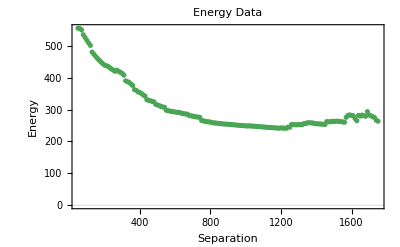

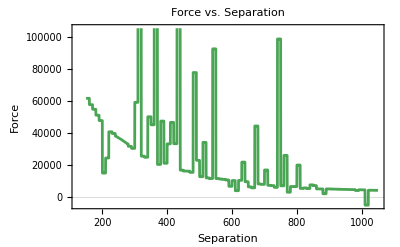

```mathematica
SolveForce[filename_] :=
Module[{stream, data,force, forcefunction, forceplot, x},
stream = OpenRead[filename];
data = ReadList[stream,{Number,Number}];
Close[stream];
data
];
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues"];
Print[SolveForce["energysep.txt"]];
allData=SolveForce["energysep.txt"];
{sep, energy}= Transpose[allData];
showData = Transpose[{sep,Map[#/(10^5)&,energy//N]}]
energyGraph = ListPlot[showData, PlotRange->All, PlotLabel->"Energy Data", PlotTheme->"Scientific", AxesLabel->{"Separation", "Energy"}, PlotStyle->Darker[Blend[{Green, LightBlue}]]]
(*ListPlot[allData,Joined->True]*)
force[x_]=-D[Interpolation[allData,InterpolationOrder->1][x],x];
forceGraph = Plot[force[x],{x,150, 1050},PlotTheme->"Scientific", AxesLabel->{"Separation", "Force"}, AxesOrigin->{125,-15}, PlotLabel->"Force vs. Separation", PlotStyle->{{Thickness[0.005],Darker[Blend[{Green, LightBlue}]]}}]
SetDirectory[StringJoin[NotebookDirectory[],"gpls/"]];
```

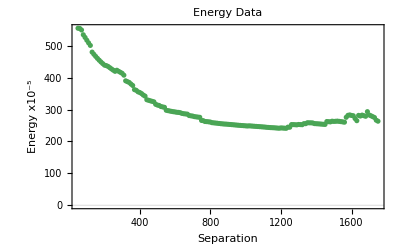

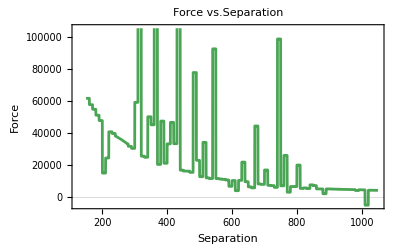

```mathematica
energyGraphnice = Show[energyGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Energy x10^("-5")],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Energy Data],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
forceGraphnice = Show[forceGraph,AxesLabel->{None,None},FrameLabel->{{HoldForm[Force],None},{HoldForm[Separation],None}},PlotLabel->HoldForm[Force vs. Separation],LabelStyle->{36,GrayLevel[0]}, ImageResolution->1200, ImageSize->Full]
```

```mathematica
SetDirectory["/home/kempsilonnaught/Builds/CellSurfaceFE-master/CellSurfaceFE/MongeParameterization/BoundaryValues/gpls/positive"];
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->20, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->{Automatic,Automatic,100}, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None];
prettyData
]
prettySurface["surface40positive.gpl"]
```

-Graphics3D-

```mathematica
prettySurface[filename_] :=
Module[{stream,data,plot1,plot2},
stream = OpenRead[filename];
Skip[stream,Record,7];
data=ReadList[stream,{Number,Number,Number}];
Close[stream];
colorScheme = ColorData["DarkRainbow"];
prettyData=ListPlot3D[data,Mesh->10, InterpolationOrder->3,ColorFunction->Function[{x, y, z},colorScheme[z]],BoxRatios->Automatic, PlotStyle->Opacity[.9], Boxed->False, Axes->False, Background->None,PlotRange->{{-300,300},{-150,150},Automatic}];
Show[prettyData,Graphics3D[{Black,Sphere[{137.5,0,400},10],Cylinder[{{-137.5,0,399},{-137.5,0,401}},10]}]]
]
prettySurface["surface5positive.gpl"]
```

-Graphics3D-

```mathematica
|
```